# Problem 3(2)

```mathematica
Integrate[(1-a)^(x-1)*a*x,{x, 1, Infinity}]
```

ConditionalExpression[(a (1-Log[1-a]))/Log[1-a]^2,Re[Log[1-a]]<0]

# Problem 4

```mathematica
Sum[Binomial[x,n]*θ^n*(1-θ)^(n-x),{x,0,n}]
```

-(-1+θ)^n+(-1+θ)^n/θ+θ^n+(-(-1+θ) θ)^n Binomial[0,n] Hypergeometric2F1[1,1,1-n,1/(1-θ)]

```mathematica
Expectation[x, x\[Distributed]BinomialDistribution[n,θ]]
```

n θ

```mathematica
Variance[BinomialDistribution[n,θ]]
```

n (1-θ) θ

# Problem 5(5)

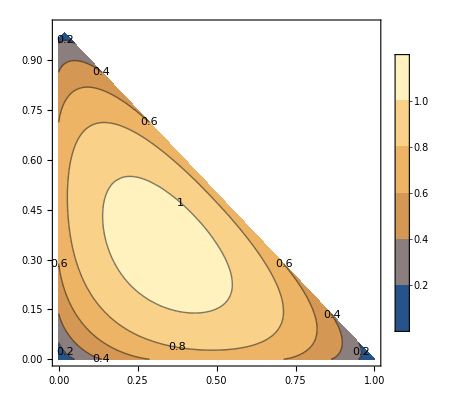

```mathematica
entropy[p1_,p2_]:= Block[{p3=1-p1-p2},-p1*Log[p1]-p2*Log[p2]-p3*Log[p3]];
ContourPlot[entropy[p1,p2], {p1,0,1}, {p2,0,1}, PlotLegends->Automatic,ContourLabels->True]
```

# Problem 6

```mathematica
data1= RandomVariate[1/100*Sum[UniformDistribution[{0,1}],{i,1,100}],1000];
data2 = RandomVariate[1/1000*Sum[UniformDistribution[{0,1}],{i,1,1000}],1000];
data3 = RandomVariate[1/10000*Sum[UniformDistribution[{0,1}],{i,1,10000}],1000];
data4 = RandomVariate[1/100000*Sum[UniformDistribution[{0,1}],{i,1,100000}],1000];
```

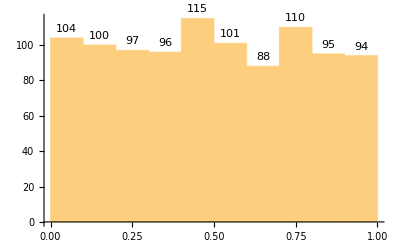

```mathematica
Histogram[data1,
LabelingFunction->Above]
```

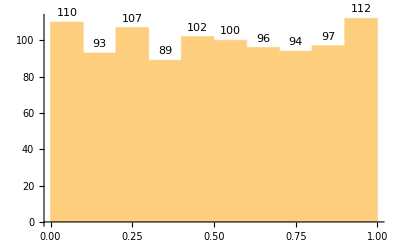

```mathematica
Histogram[data2,
LabelingFunction->Above]
```

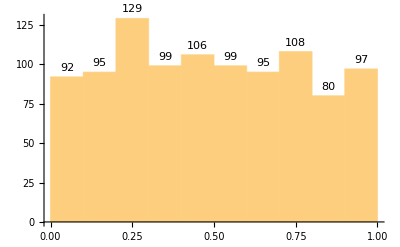

```mathematica
Histogram[data3,
LabelingFunction->Above]
```

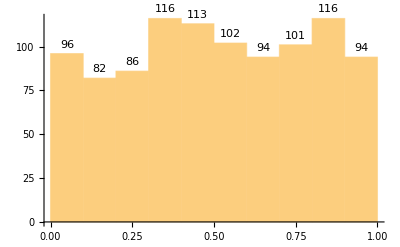

```mathematica
Histogram[data4,
LabelingFunction->Above]
```

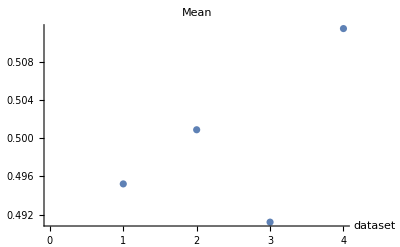

```mathematica
ListPlot[{Mean[data1],Mean[data2],Mean[data3],Mean[data4]},AxesLabel->{dataset},PlotLabel->"Mean"]
```

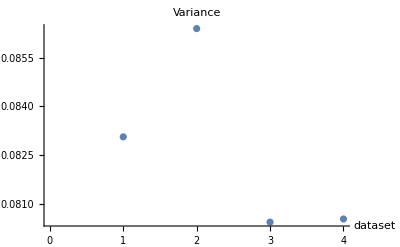

```mathematica
ListPlot[{Variance[data1],Variance[data2],Variance[data3],Variance[data4]},
			AxesLabel->{dataset},PlotLabel->"Variance"]
```

```mathematica
Log[1000.]
```

6.90776